## Projections

```mathematica
With[{context="projections`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
c1={1,1}/Sqrt[2]
c2=c1*{1,-1}
```

{1/(√2),1/(√2)}

{1/(√2),-1/(√2)}

```mathematica
v={2,3}
```

{2,3}

```mathematica
{v.c1, v.c2}
```

{3/(√2)+√2,-3/(√2)+√2}

```mathematica
Simplify[(v.c1)c1+(v.c2)c2]
```

{2,3}

```mathematica
With[{context="projections`"},If[Context[]==context,End[],"Not in context"]]
```

projections`

## DFT

```mathematica
With[{context="dft`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
data=Cos[Pi/4*Range[0,63]]
```

{1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2)}

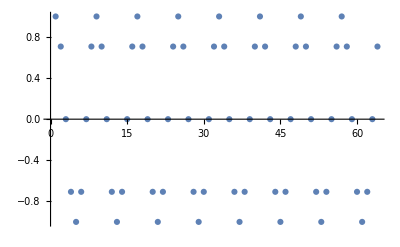

```mathematica
ListPlot[data]
```

```mathematica
MatrixForm@{Fourier[data]}
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Simplify[Cos[θ]-1/2(Exp[I θ]+Exp[- I θ])]
```

0

```mathematica
With[{context="dft`"},If[Context[]==context,End[],"Not in context"]]
```

dft`

## Sound Alteration

```mathematica
With[{context="alter`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/eric/Documents/School/QEA2/Acoustic Modem/Bset 1

```mathematica
playSound[data_]:=Module[{path="/tmp/sound.wav"},Export[path,data];SystemOpen[path]]
playSound[data_,fs_]:=playSound[Sound@SampledSoundList[data,fs]]
```

```mathematica
ExampleData["Audio"]
```

{{Audio,Apollo11ReturnSafely},{Audio,Apollo11SmallStep},{Audio,BalloonPop},{Audio,Bee},{Audio,Bird},{Audio,BlackcapWarbler},{Audio,Cat},{Audio,Cello},{Audio,CelloScale},{Audio,ChurchBell},{Audio,Clapping},{Audio,CreakyDoor},{Audio,Crowd},{Audio,DogBark},{Audio,Drums},{Audio,FemaleVoice},{Audio,Flute},{Audio,FluteScale},{Audio,FogHorn},{Audio,IRMaesHowe},{Audio,IRRailwayTunnel},{Audio,IRSportsCenter},{Audio,IRStairway},{Audio,IRStAndrewsChurch},{Audio,IRStMarysChurch},{Audio,IRYorkMinsterChurch},{Audio,Laughing},{Audio,MaleVoice},{Audio,NoisyTalk},{Audio,Piano},{Audio,PianoScale},{Audio,PowerSupply},{Audio,Scream},{Audio,SubwayTrain},{Audio,Sword},{Audio,ThaiBells},{Audio,Water},{Audio,Wind}}

### One Small Step

```mathematica
fs=ExampleData[{"Audio","Apollo11SmallStep"},"SampleRate"]
```

22050

```mathematica
data=ExampleData[{"Audio","Apollo11SmallStep"},"Data"];
```

```mathematica
playSound[data,fs]
```

```mathematica
fft = Fourier[data];
```

```mathematica
Rasterize@ListLinePlot[Abs@fft,PlotRange->Full]
```

-Graphics-

Perform filtering: Note that I am cutting out a higher frequency than the Bset recommends because my audio sample is different.

```mathematica
filteredFourier=fft;
cutoff = Round[Length@fft/10];
filteredFourier[[cutoff;;-cutoff]]=fft[[cutoff;;-cutoff]]/10;
```

```mathematica
Rasterize@ListLinePlot[Abs[filteredFourier[[;;;;3]]],PlotRange->Full]
```

-Graphics-

Convert back to sound

```mathematica
data2 = Re@InverseFourier[filteredFourier];
playSound[data2,fs]
```

### Guitar

```mathematica
fs=Import["provided files/guitar_riff_hum.wav","SampleRate"]
data=Import["provided files/guitar_riff_hum.wav","Data"];
```

44100

```mathematica
playSound[data,fs]
```

```mathematica
fft = Fourier[data];
```

```mathematica
Rasterize@ListLinePlot[Abs@fft,PlotRange->Full]
```

-Graphics-

Perform filtering: Looking at the graph above, I decided to neuter all overpowered freqs.

```mathematica
badFreq = Max
```

```mathematica
cutoff = 3;
filteredFourier=Map[Function[val,If[Abs@val>cutoff,0,val]],fft];
```

```mathematica
Rasterize@ListLinePlot[Abs[filteredFourier],PlotRange->Full]
```

-Graphics-

Convert back to sound

```mathematica
data2 = Re@InverseFourier[filteredFourier];
playSound[data2,fs]
```

### Wrap up

```mathematica
With[{context="alter`"},If[Context[]==context,End[],"Not in context"]]
```

alter`

## Template

```mathematica
With[{context="xxx"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{context="xxx"},If[Context[]==context,End[],"Not in context"]]
```

Not in context

## Scratch work

```mathematica
Export["Mathematica Scratch.pdf",EvaluationNotebook[]]
```

Mathematica Scratch.pdf